```mathematica
SetDirectory[NotebookDirectory[]];
```

# h_scaling

## data

```mathematica
mpi=Flatten[Import["../LPAp_mpi/buffer/mPion.dat"]];
fpi=Flatten[Import["../LPAp_mub0/buffer/fpi.dat"]];
Zphi=Flatten[Import["../LPAp_mub0/buffer/Zphi.dat"]];
fpi=fpi/√Zphi;
h=Flatten[Import["../LPAp_mub0/buffer/c.dat"]]*197.33^3;
datamub0=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
datamub0linear=Transpose[{h[[2;;Length[h]]],fpi[[2;;Length[h]]]}];

mpi=Flatten[Import["../LPAp_mpi/buffer/mPion.dat"]];
fpi=Flatten[Import["../LPAp_mub500/buffer/fpi.dat"]];
Zphi=Flatten[Import["../LPAp_mub500/buffer/Zphi.dat"]];
fpi=fpi/√Zphi;
h=Flatten[Import["../LPAp_mub500/buffer/c.dat"]]*197.33^3;
datamub500=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
datamub500linear=Transpose[{h[[2;;Length[h]]],fpi[[2;;Length[h]]]}];
```

## Pre Fit

```mathematica
fitb=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fita=Transpose[{Log[h[[2;;Length[h]-2]]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[h]-2}]]}];
```

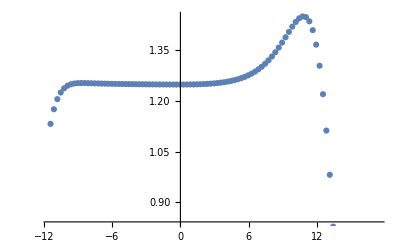

```mathematica
Show[ListPlot[fita],ListLinePlot[{{-11,1.534},{20,1.534}},PlotStyle->Red]]
```

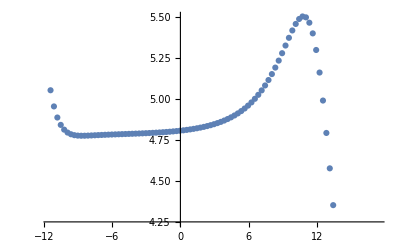

```mathematica
ListPlot[fitb]
```

## Fit

```mathematica
(*A=Exp[1.532];*)
δ=4.79;
delta=4.79;
beta=0.397;
nu=0.759;
omega=0.6745;
θH=(nu*omega)/(beta*delta);
fitfun=A x^(1/δ)(1+am x^θH);
fitfun2=A x^(1/δfit)(1+am x^θH);
fitfun3=A+1/δfit x+Log[1+am Exp[x]^θH];
fitfun4=A1 x^(1/delta)(1+am1 x^θH1);
```

```mathematica
fitdelta=Transpose[{h[[3;;Length[h]-3]],Flatten[Table[NonlinearModelFit[datamub0linear[[i-2;;i+2]],fitfun2,{A,δfit,am},x][[1]][[2]][[2]][[2]],{i,3,Length[h]-3}]]}];
fitdelta2=Transpose[{h[[2;;Length[h]-2]],Flatten[Table[NonlinearModelFit[datamub0[[i-1;;i+1]],fitfun3,{A,δfit,am},x][[1]][[2]][[2]][[2]],{i,2,Length[h]-2}]]}];
```

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

NonlinearModelFit::nrlnum: 在 {A,δfit,am} = {2.16472,1.69058,-2.18536} 处，函数值 {-3.2283+3.14159 ⅈ,-2.0345+3.14159 ⅈ,-1.37993+3.14159 ⅈ} 不是由实数组成的维度为 {3} 的列表.

NonlinearModelFit::nrlnum: 在 {A,δfit,am} = {2.37073,1.66486,-2.60493} 处，函数值 {-0.882323+3.14159 ⅈ,-0.484221+3.14159 ⅈ,-0.131415+3.14159 ⅈ} 不是由实数组成的维度为 {3} 的列表.

NonlinearModelFit::nrlnum: 在 {A,δfit,am} = {2.64786,1.62969,-3.16595} 处，函数值 {0.283522+3.14159 ⅈ,0.580571+3.14159 ⅈ,0.862959+3.14159 ⅈ} 不是由实数组成的维度为 {3} 的列表.

General::stop: 在本次计算中，NonlinearModelFit::nrlnum 的进一步输出将被抑制.

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

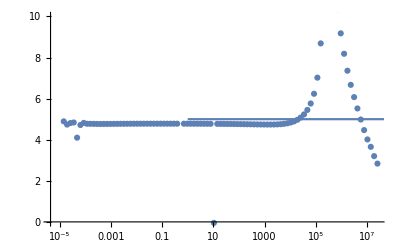

```mathematica
Show[ListPlot[fitdelta,ScalingFunctions->{"Log"},PlotRange->{All,{0,10}}],ListLinePlot[{{0.001,5},{1000,5}}]]
```

```mathematica
fitdeltampi=Transpose[{mpi[[3;;Length[h]-3]],Transpose[fitdelta][[2]]}];
```

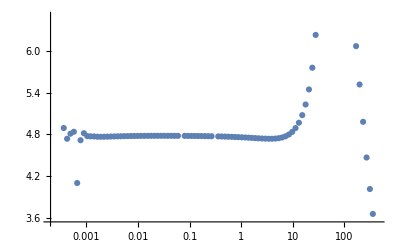

```mathematica
Show[ListPlot[fitdeltampi,ScalingFunctions->{"Log"}]]
```

```mathematica
Export["NLOdelta.dat",fitdeltampi]
```

NLOdelta.dat

## Fit mub

```mathematica
(*A=Exp[1.532];*)
δ=4.79;
delta=4.79;
beta=0.397;
nu=0.759;
omega=0.6745;
θH=(nu*omega)/(beta*delta);
fitfun=A x^(1/δ)(1+am x^θH);
fitfun2=A x^(1/δfit)(1+am x^θH);
fitfun3=A+1/δfit x+Log[1+am Exp[x]^θH];
fitfun4=A1 x^(1/delta)(1+am1 x^θH1);
```

```mathematica
fitdeltamub500=Transpose[{h[[3;;Length[h]-3]],Flatten[Table[NonlinearModelFit[datamub500linear[[i-2;;i+2]],fitfun2,{A,δfit,am},x][[1]][[2]][[2]][[2]],{i,3,Length[h]-3}]]}];
```

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

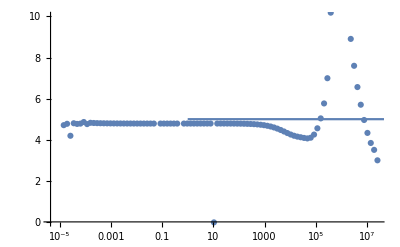

```mathematica
Show[ListPlot[fitdeltamub500,ScalingFunctions->{"Log"},PlotRange->{All,{0,10}}],ListLinePlot[{{0.001,5},{1000,5}}]]
```

```mathematica
fitdeltampimub500=Transpose[{mpi[[3;;Length[h]-3]],Transpose[fitdeltamub500][[2]]}];
```

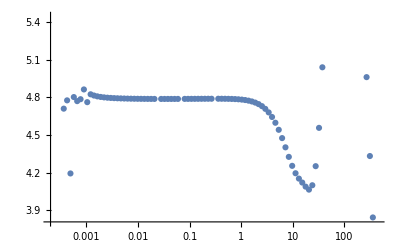

```mathematica
Show[ListPlot[fitdeltampimub500,ScalingFunctions->{"Log"}]]
```

```mathematica
Export["NLOdeltamub500.dat",fitdeltampimub500]
```

NLOdeltamub500.dat